Piecewise[{{-1/Abs[r], r^2>0.01}, {-10.-√(0.01-r^2), True}}]

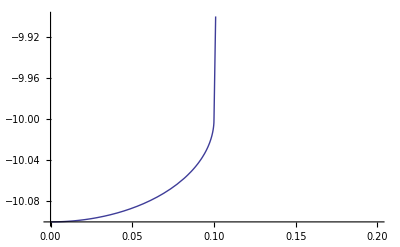
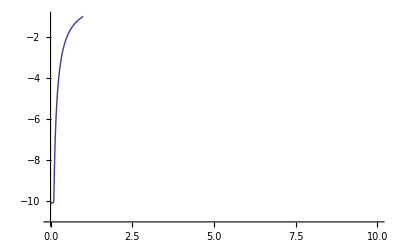

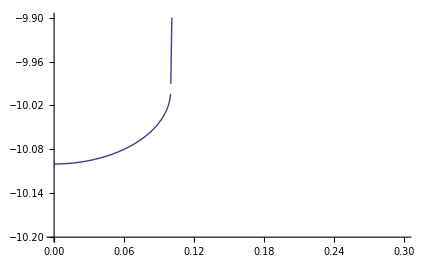

```mathematica
Clear[e, v] ;
e = 0.1 ;
v[r_] = Piecewise[ {{-1/Abs[r], r^2 > e^2}}, -1/e - Sqrt[e^2 - r^2] ]

(* http://mathematica.stackexchange.com/questions/13657/plot-showing-discontinuity-where-it-shouldnt *)
{Plot[ v[r], {r, 0, 0.2} , PlotRange -> {Full, {-10.1, -9.9}},Exclusions->None],
Plot[ v[r], {r, 0, 2} , PlotRange -> {{0, 10}, {-11, -1}},Exclusions->None] }
(*Plot[ v[r], {r, 0, 0.3} ]
v[e]*)
```